```mathematica
ClearAll["Global`*"]
```

## Initialize polymer

```mathematica
InitializeStraightPolymer[N_]:=ConstantArray[0,N-1]
```

```mathematica
InitializeBentPolymer[N_]:=ConstantArray[π/10,N-1]
```

## Compute total energy

```mathematica
TotalEnergy[θ_,κ_,b_]:=κ/(2b)Total[θ^2]
```

## Plot polymer

```mathematica
θ={0,Pi/2,-Pi/2,Pi/6,Pi/2, -Pi/2}; (*for testing*)
```

```mathematica
ChainPlot[Angles_,b_]:=Module[{},
current={0,0};
PointsList={{0,0}};
For[i=1,i<=Length[Angles],i++, next=current+b*{Cos[Total[Angles[[;;i]]]],Sin[Total[Angles[[;;i]]]]};current=next;AppendTo[PointsList,current]];
ListLinePlot[PointsList, PlotRange->All]
]
```

```mathematica
ChainPlot[θ,1]; (*for testing*)
```

## Monte Carlo method

```mathematica
old[n_]:=InitializeBentPolymer[n]; (*initialize polymer of size n, either bent or straight*)
```

```mathematica
metropolis2[nsegments_,nsteps_,nwrite_,κ_,b_,β_,x_,y_]:=Module[{},
EnergyList={TotalEnergy[old[nsegments],κ,b]}; (*energy at beginning*)
OldAngles=old[nsegments]; (*initialize angles*)
OldEnergy=TotalEnergy[old[nsegments],κ,b]; (*set old energy*)
Do[{r=RandomInteger[{1,nsegments-1}];
OriginalAngle=OldAngles[[r]]; (*pick random angle*)
p=RandomReal[{x,y}];(*set pertubation*)
ΔE=κ/(2b)(2OriginalAngle p+p^2); (*calculate ΔE*)
If[RandomReal[]≤Min[{1,Exp[-β*ΔE]}], (*acceptance probability*)
{NewAngles=ReplacePart[OldAngles,r->OriginalAngle+p], (*update angles*)
NewEnergy=OldEnergy+ΔE (*update energy*)
},
{NewAngles=OldAngles, (*re-use same angles*)
NewEnergy=OldEnergy}]; (*don't update energy*)
If[Mod[i,nwrite]==0,AppendTo[EnergyList,NewEnergy]]; (*only append all nwrite energy values to list - done for memory saving*)
OldEnergy=NewEnergy; (*set energy for next iteration*)
OldAngles=NewAngles; (*set angles for next iteration*)
},{i,1,nsteps}]; 
EnergyList]
```

## Numerical analysis

```mathematica
T2=Table[{q,Timing[metropolis2[20,10^q,1000,1,.05,1,-.01,.01]][[1]]},{q,4,7,.5}];
```

{{4.,0.17969},{4.5,0.529491},{5.,1.71458},{5.5,5.69478},{6.,17.499},{6.5,54.5073},{7.,169.779}}

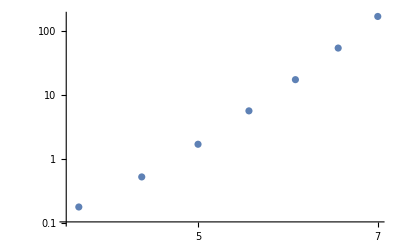

```mathematica
ListLogLogPlot[T2]
```

## Find τ_eq

```mathematica
EnergyListBent=metropolis2[20,3*10^5,100,1,.05,1,-.01,.01]; (*Energy list with bent initial polymer*)
```

```mathematica
EnergyListStraight=metropolis2[20,3*10^5,100,1,.05,1,-.01,.01]; (*Energy list with straight initial polymer*)
```

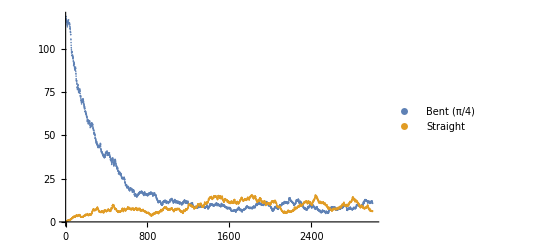

```mathematica
ListPlot[{EnergyListBent,EnergyListStraight}, PlotRange->All,PlotLegends->Placed[{"Bent (π/4)","Straight"},{0.85,0.85}]
] (*Plot to visualize*)
```

```mathematica
Export["energydata1.xls",EnergyList]; (*For bent polymer to find tau_eq*)
```

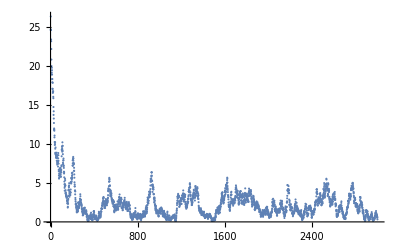

```mathematica
ListPlot[metropolis2[5,3*10^5,100,1,.05,1,-.01,.01],PlotRange->All]
```

```mathematica
(*same for N=50 and b = 0.02*)
```

```mathematica
EnergyListBent2=metropolis2[50,3*10^5,100,1,.02,1,-.01,.01];
```

```mathematica
EnergyListStraight2=metropolis2[50,3*10^5,100,1,.02,1,-.01,.01];
```

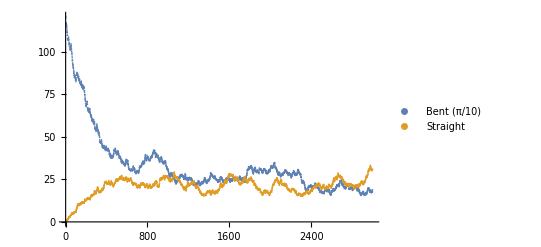

```mathematica
ListPlot[{EnergyListBent2,EnergyListStraight2}, PlotRange->All,PlotLegends->Placed[{"Bent (π/10)","Straight"},{0.85,0.85}]
]
```

```mathematica
Export["energydata2.xls",EnergyListBent2];
```

## Get persistence length

```mathematica
(*same as metropolis2, but now average cosine of angle is outputted*)
metropolis3[nsegments_,nsteps_,nwrite_,κ_,b_,β_,x_,y_]:=Module[{},
EnergyList={TotalEnergy[old[nsegments],κ,b]};
OldAngles=old[nsegments];
OldEnergy=TotalEnergy[old[nsegments],κ,b];
AverageCosList={Mean[Cos[OldAngles]]};
Do[{r=RandomInteger[{1,nsegments-1}];
OriginalAngle=OldAngles[[r]];
p=RandomReal[{x,y}];
ΔE=κ/(2b)(2OriginalAngle p+p^2);
If[RandomReal[]≤Min[{1,Exp[-β*ΔE]}],{NewAngles=ReplacePart[OldAngles,r->OriginalAngle+p],NewEnergy=OldEnergy+ΔE},{NewAngles=OldAngles,NewEnergy=OldEnergy}];
If[Mod[i,nwrite]==0,AppendTo[EnergyList,NewEnergy];AppendTo[AverageCosList,Mean[Cos[NewAngles]]]];
OldEnergy=NewEnergy;
OldAngles=NewAngles;
},{i,1,nsteps}];
AverageCosList]
```

```mathematica
metropolis3[50,10^7,30000,1,0.02,0.5,-0.01,0.01];  (*run metropolis3*)
```

```mathematica
AverageCosListEq=Drop[AverageCosList,6]; (*drop first 6*30000 averages to make sure we only consider equilibrium values*)
cos2d=Mean[AverageCosListEq] (*calculate average cosine*)
persistance=0.02/(2*(1-cos2d)) (*calculate persistence length*)
```

## Error analysis

```mathematica
EnergyList50 = metropolis2[50,10^7,5000,1,.02,1,-.01,.01];
```

```mathematica
EnergyList50Drop = Drop[EnergyList50,6];
```

```mathematica
beta = 1;
```

```mathematica
SdtDev = N[Sqrt[49/(2*beta^2)]] (*using theoretical value for variance found*)
StandardDeviation[EnergyList50Drop ](*calculating actual standard deviation of the list*)
```

4.94975

5.05545